## Schroedinger problem

```mathematica
Unprotect@Print;
Print = Null;
<<xAct`xPert`;
<<xAct`xPand`;
<<xAct`SplitExpression`.1d ;
(* Define a 5d manifold M *)
DefManifold[M,5,{a,b,c,d,e,n,p,q,s,t}];
(* We also define a metric on this manifold,with negative determinant and associated covariant derivative CD.This derivative is extended to act on tensor densities defined using the determinant of the metric g in the basis AIndex: *)
DefMetric[-1,g[-a,-b],CD,{";","∇"},WeightedWithBasis->AIndex];
DefParameter[z];
(* Use the same notation as Alfonso *)
$CovDFormat="Prefix";
(* Because we shall work with a single covariant derivative operator,we can choose a simpler output for the geometric tensors *)
PrintAs[RiemannCD]^="R";
PrintAs[RicciCD]^="R";
PrintAs[RicciScalarCD]^="R";
PrintAs[ChristoffelCD]^="Γ";
PrintAs[EinsteinCD]^="G";
(* define the warp factor as a order zero tensor *)
DefTensor[A[],M];
(* Definition of the Dilaton field Φ *)
DefTensor[Phi[],M,PrintAs->"Φ"];
(* Definition of the scalar field ϕ *)
DefTensor[phi[],M,PrintAs->"ϕ"]
(* colour in blue the perturbative orders *)
Unprotect[IndexForm];
IndexForm[LI[x_]]:=ColorString[ToString[x],RGBColor[0,0,1]];
Protect[IndexForm];
(* splitting code *)
DefManifold[flat,4,{μ,ν,ρ,σ,λ}];
DefMetric[-1,η[-μ,-ν],CDflat,{"|","𝒟"}];
η/:PD[_][η[__]]:=0;
(* explicit set the non-z dependence of A and Φ to improve computations *)
A/:PD[p_|-p_][A[]]/;MemberQ[IndicesOfVBundle@VBundleOfMetric[η],p,Infinity]:=0;
Phi/:PD[p_|-p_][Phi[]]/;MemberQ[IndicesOfVBundle@VBundleOfMetric[η],p,Infinity]:=0;
DefConstantSymbol[{m}]
DefSplitting[AAdS,M->{z,flat}];
SplittingRules[AAdS,
{g[-z,-z]->Exp[2A[]],
g[-z,-μ]->0,
g[-μ,-z]->0,
g[-μ,-ν]->Exp[2A[]]η[-μ,-ν],
g[z,z]->Exp[-2A[]],
g[z,μ]->0,
g[μ,z]->0,
g[μ,ν]->Exp[-2A[]]η[μ,ν]
}
];
(* define that the following tensor depends on z, THIS HAS TO BE DEFINED BEFORE THE COMPUTING THE CURVATURES *)
AddTensorDependencies[{g,A,Phi,phi},{z}];
(* Define metric perturbation *)
DefMetricPerturbation[g,h,ϵ];
DefTensorPerturbation[δΦ[LI[order]],Phi[],M];
DefTensorPerturbation[δϕ[LI[order]],phi[],M];
time=ComputeCurvatureTensors[AAdS]//Timing//First;
Unprotect[Print];
Print=.;
Protect[Print];
Print["Splitting curvature tensors computed in ", time, " seconds"]
```

Splitting curvature tensors computed in 0.894157 seconds

```mathematica
(* Definition of the lagrangian density *)
Lagrangian=-1/2 √(-Detg[])Exp[-Phi[]](CD[-a]@phi[]CD[a]@phi[]+m^2 phi[]*phi[]);
```

```mathematica
(* Obtaining the equations of motion *)
ExpandPerturbation@Perturbation@Lagrangian/.h[__]->0/.δΦ[_]->0//ContractMetric//Simplification;
VarD[δϕ[LI[1]],CD][%]/.delta[Times[-1,LI[1]],LI[1]]->1//Simplification;
eom=%/(√(-Detg[]))
```

ⅇ^-Φ (-m^2 ϕ+∇_a ∇^a ϕ-∇_a Φ ∇^a ϕ)

```mathematica
(* Now let's split this expression *)
SplitExpression[AAdS,Fun->SeparateMetric[],ComponentsListQ->True][∇_a ∇^a ϕ-∇_a Φ ∇^a ϕ]
```

∇_a ∇^a ϕ-∇_a Φ ∇^a ϕ→3 ⅇ^(-2 A) ∂_z A ∂_z ϕ-ⅇ^(-2 A) ∂_z ϕ ∂_z Φ+ⅇ^(-2 A) ∂_z ∂_z ϕ+ⅇ^(-2 A) ∂_λ ∂^λ ϕ

```mathematica
Exp[-Phi[]](3 ⅇ^(-2 A) D[A, z] D[ϕ, z]-ⅇ^(-2 A) D[ϕ, z] D[Φ, z]+ⅇ^(-2 A) ∂_z ∂_z ϕ+ⅇ^(-2 A) ∂_λ ∂^λ ϕ)-m^2 ϕ ⅇ^-Φ//Simplify;
Exp[Phi[]+2A[]]%//.{∂_λ ∂^λ ϕ->-k^2 phi[],ParamD[z][Phi[]]->Φ'[x],ParamD[z][A[]]->B'[x],ParamD[z][phi[]]->f'[x],ParamD[z,z][phi[]]->f''[x],A[]->B[x],phi[]->f[x]};
eomFT=%
```

-k^2 f[x]-ⅇ^(2 B[x]) m^2 f[x]+3 B'[x] f'[x]-f'[x] Φ'[x]+f''[x]

```mathematica
(* Writing this equation as a Sturm-Liouville problem *)
eomSL=Exp[3B[x]-Φ[x]]eomFT//Expand
```

-ⅇ^(3 B[x]-Φ[x]) k^2 f[x]-ⅇ^(5 B[x]-Φ[x]) m^2 f[x]+3 ⅇ^(3 B[x]-Φ[x]) B'[x] f'[x]-ⅇ^(3 B[x]-Φ[x]) f'[x] Φ'[x]+ⅇ^(3 B[x]-Φ[x]) f''[x]

```mathematica
(* Writing the last equation in Schrodinger form *)
eomFT/.f->Function[x,ⅇ^Q[x] F[x]]//Collect[#,{F[x],F'[x],F''[x]}]&;
Qrule=DSolve[3B'[x]+2Q'[x]-Φ'[x]==0,Q,x][[1]];
eomFT/.f->Function[x,ⅇ^Q[x] F[x]]/.Qrule//Collect[#,{F[x],F'[x],F''[x]},Simplify]&;
%/Coefficient[%,F''[x]]//Collect[#,{F[x],F'[x],F''[x]},Simplify]&
```

Attributes::notfound: Symbol DSolveDispatchODE not found.

F''[x]+1/4 F[x] (-4 k^2-4 ⅇ^(2 B[x]) m^2-9 B'[x]^2+6 B'[x] Φ'[x]-Φ'[x]^2-6 B''[x]+2 Φ''[x])

## Normalizable modes Boundary Conditions

```mathematica
(* Let's find the normalizable mode of a scalar field in AdS. We try to get the result in page 7 of the paper 1307.0009. This result is valid for a proton k^2=-1, that in d = 4 and Δ = 9/2 gives m^2= 9/4 *)
eom=f[x]-ⅇ^(2 B[x]) m^2 f[x]+3 B'[x] f'[x]-f'[x] Φ'[x]+f''[x]/.{m^2->9/4,B->(-Log[#]&),Φ->(0#&)}
solAdS=DSolve[%==0,f,x][[1]]//FullSimplify[#,Assumptions->{x>0,k<0}]&
```

f[x]-(9 f[x])/(4 x^2)-(3 f'[x])/x+f''[x]

{f→Function[{x},√(2/π) x^(3/2) C[1] (-(3 Cos[x])/x-Sin[x]+(3 Sin[x])/x^2)+√(2/π) x^(3/2) C[2] (Cos[x]-(3 Cos[x])/x^2-(3 Sin[x])/x)]}

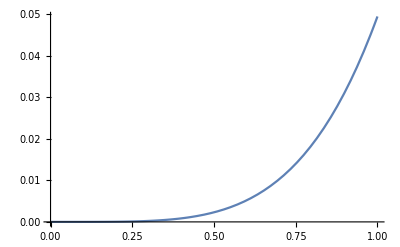

```mathematica
(* So the normalizable mode is C[1]->1 and C[2]->0*)
Plot[f[z]/.solAdS/.{C[1]->1,C[2]->0},{z,0,1}]
```

```mathematica
(* Now let's see how it falls near z = 0. *)
Series[f[z]/.solAdS/.{C[1]->1,C[2]->0},{z,0,5}]
```

1/15 √(2/π) z^(9/2)+O[z]^(11/2)

```mathematica
(* It indeed falls as z^(9/2). So Δ is 9/2, since a normalizable mode falls as 9/2. *)
```

```mathematica
(* What is the value of the derivative near the boundary? *)
Series[f'[z]/.solAdS/.{C[1]->1,C[2]->0},{z,0,5}]
```

(3 z^(7/2))/(5 √(2 π))+O[z]^(11/2)

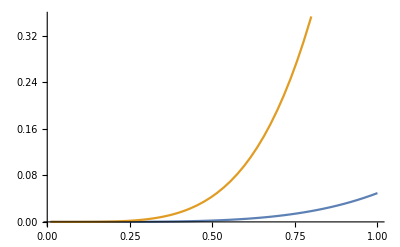

```mathematica
(* So we should give as boundary conditions f(ϵ)=ϵ^(9/2) and f'(ϵ)=9/2 ϵ^(7/2). Let's try to solve this numerically. I expect a difference between the analytical and numeric solutions because of pi factors that i do not include in the BC in the numerical routine *)
ϵ=0.01;
solAdSNum=NDSolve[{eom==0,f[ϵ]==ϵ^(9/2),f'[ϵ]==9/2 ϵ^(7/2)},f,{x,ϵ,1}][[1]];
Plot[{f[x]/.solAdS/.{C[1]->1,C[2]->0},f[x]/.solAdSNum},{x,ϵ,1}]
```

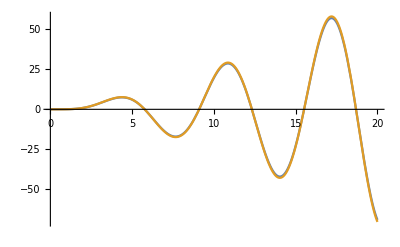

19.3108

19.6678

1.84896

```mathematica
(* Now I try to get the solution with the exact numerical factos. It is expected to have agreement *)
ϵ=0.01;
solAdSNum=NDSolve[{eom==0,f[ϵ]==1/15 √(2/π)ϵ^(9/2),f'[ϵ]==3/(5 √(2 π))ϵ^(7/2)},f,{x,ϵ,20},PrecisionGoal->20][[1]];
(* We compare these solutions graphically and through the evaluation of an integral - necessary later for this project *)
Plot[{f[x]/.solAdS/.{C[1]->1,C[2]->0},f[x]/.solAdSNum},{x,ϵ,20}]
i1=NIntegrate[f[x]/.solAdS/.{C[1]->1,C[2]->0},{x,ϵ,20}]
i2=NIntegrate[f[x]/.solAdSNum,{x,ϵ,20}]
(* I tried different limits of integrations, the overall error is 2 %. *)
Abs[i1-i2]/Abs[i1]*100
```

```mathematica
(* REMEMBER THAT THERE IS STILL AN OVERALL CONSTANT TO FIX! This will be fixed by demanding the integral ∫dz fn(z) fm(z) w(z) = 1 in the warped-AdS case. *)
```

```mathematica
f[z]/.solAdS/.{C[2]->0}
Solve[Integrate[%^2/z^3,{z,0,zm}]==1,C[1]]//FullSimplify[#,Assumptions->{zm>0}]&
```

√(2/π) z^(3/2) C[1] (-(3 Cos[z])/z-Sin[z]+(3 Sin[z])/z^2)

{{C[1]→-(√(2 π))/(√(-(6+6 zm^2-2 zm^4+6 (-1+zm^2) Cos[2 zm]+zm (-12+zm^2) Sin[2 zm])/zm^3))},{C[1]→(√(2 π))/(√(-(6+6 zm^2-2 zm^4+6 (-1+zm^2) Cos[2 zm]+zm (-12+zm^2) Sin[2 zm])/zm^3))}}

## Bulk-to-boundary propagator

```mathematica
(* This computations are a replication of the ones found in the paper "Structure of vector mesons in a holographic model with linear confinement" *)
```

```mathematica
ClearAll[eom];
eom =D[1/z Exp[-z^2]D[v[z],z],z]+p^2 1/z Exp[-z^2]v[z]
(* Now I write the EOM in Schrodinger form *)
eom/.{v->(Exp[B[#]]V[#]&)}//Expand;
%/Coefficient[%,V''[z]]//Collect[#,{V[z],V'[z],V''[z]},Simplify]&//Coefficient[#,V'[z]]&;
Brule=DSolve[%==0,B,z][[1]]/.{C[1]->0};
eom/.{v->(Exp[B[#]]V[#]&)}/.Brule//Collect[#,{V[z],V'[z],V''[z]},Simplify]&;
schProb=(-%/Coefficient[%,V''[z]]//FullSimplify)==0
```

(ⅇ^(-z^2) p^2 v[z])/z-2 ⅇ^(-z^2) v'[z]-(ⅇ^(-z^2) v'[z])/z^2+(ⅇ^(-z^2) v''[z])/z

(-p^2+3/(4 z^2)+z^2) V[z]-V''[z]==0

```mathematica
(* Now we solve the Schrodinger problem. For some reason in the literature people only pick the Laguerre solution. *)
schSol=DSolve[{schProb/.p^2->4(n+1)},V,z][[1]]/.{C[1]->0,2C[2]->C[2]}//FullSimplify
Ψ[n_,z_]:=ⅇ^(-z^2/2) z^(3/2) √(2/(n+1))LaguerreL[n,1,z^2]
ψ[n_,z_]:=z^2 √(2/(n+1)) LaguerreL[n,1,z^2]
```

{V→Function[{z},2 ⅇ^(-z^2/2) z^(3/2) 0 HypergeometricU[-n,2,z^2]+ⅇ^(-z^2/2) z^(3/2) LaguerreL[n,1,z^2] C[2]]}

```mathematica
Series[Ψ[n,z],{z,0,2}]//FullSimplify[#,Assumptions->{n≥0}]&
```

√2 √(1+n) z^(3/2)+O[z]^(5/2)

```mathematica
(* Now we solve equation 10 *)
DSolve[{eom==0},v,z][[1]]//FullSimplify[#,Assumptions->{p^2≥0}]&
```

{v→Function[{z},z^2 C[1] Hypergeometric1F1[1-p^2/4,2,z^2]+C[2] MeijerG[{{},{1/4 (4+p^2)}},{{0,1},{}},-z^2]]}

```mathematica
Limit[z^2 Hypergeometric1F1[1-p^2/4,2,z^2],z->0]
Limit[MeijerG[{{},{1/4 (4+p^2)}},{{0,1},{}},-z^2],z->0]
```

0

1/Gamma[1+p^2/4]

```mathematica
eom
```

(ⅇ^(-z^2) p^2 v[z])/z-2 ⅇ^(-z^2) v'[z]-(ⅇ^(-z^2) v'[z])/z^2+(ⅇ^(-z^2) v''[z])/z